# First Contours

```mathematica
plot=Plot3D[-E^(-x^2) * Sin[y],{x,-2,2},{y,0,2Pi}];
```

Taken from https://mathematica.stackexchange.com/questions/14863/placing-a-contourplot-under-a-plot3d

```mathematica
contourPotentialPlot1=ContourPlot[-3600. h^2+0.02974 h^4-5391.90 s^2+0.275 h^2 s^2+0.125 s^4,{h,-400,400},{s,-300,300},PlotRange->{-1.4*10^8,2*10^7},Contours->15,Axes->False,PlotPoints->30,PlotRangePadding->0,Frame->False,ContourShading->None];

potential1=Plot3D[-3600. h^2+0.02974 h^4-5391.90 s^2+0.275 h^2 s^2+0.125 s^4,{h,-400,400},{s,-300,300},PlotRange->{-1.4*10^8,2*10^7},ClippingStyle->None,MeshFunctions->{#3&},Mesh->15,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.3],Blue},{Opacity[.2],Blue}},Lighting->"Neutral"];

level=-1.2 10^8;gr=Graphics3D[{Texture[contourPotentialPlot1],EdgeForm[],Polygon[{{-400,-300,level},{400,-300,level},{400,300,level},{-400,300,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"];

Show[potential1,gr,PlotRange->All,BoxRatios->{1,1,.6}]
```

-Graphics3D-

# CONTOURS

-Graphics3D-

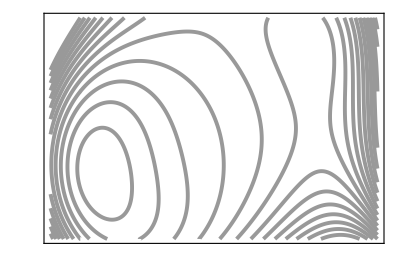

```mathematica
f[x_,y_]=(-(x-3)^3 -(y-2)^3 +4)(-(x-1)^2 - (y-1)^2+2);
Plot3D[f[x,y],{x,0,8},{y,0,6}]
ContourPlot[f[x,y],{x,-.5,5},{y,0,3},AspectRatio->2/3,Contours->Join[Table[i,{i,0,100,10}],Table[i,{i,-100,0,10}]],ContourShading -> None,  AspectRatio -> 2/3,TicksStyle -> Large,
  ContourStyle -> {{Thickness[.007], GrayLevel[.6]}}, 
  PlotPoints -> 100,FrameTicks->None]
```